```mathematica
sol=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==1},y,x]
sol1=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==0},y,x]
sol2=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==-6},y,x]
sol3=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==-1},y,x]
sol4=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==6},y,x]
sol5=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==3},y,x]
```

{{y→Function[{x},-ⅇ^x (-3+2 x)]}}

{{y→Function[{x},-3 ⅇ^x (-1+x)]}}

{{y→Function[{x},-3 ⅇ^x (-1+3 x)]}}

{{y→Function[{x},-ⅇ^x (-3+4 x)]}}

{{y→Function[{x},3 ⅇ^x (1+x)]}}

{{y→Function[{x},3 ⅇ^x]}}

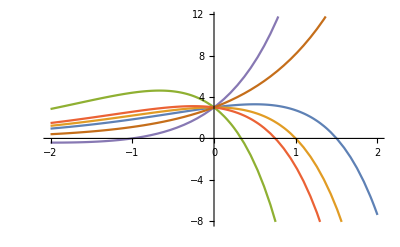

```mathematica
Plot[{ -ⅇ^x (-3+2 x), -3 ⅇ^x (-1+x),-3 ⅇ^x (-1+3 x),  -ⅇ^x (-3+4 x),3 ⅇ^x (1+x), 3 ⅇ^x  }, {x,-2,2}, BaseStyle->{FontSize->14, FontWeight->Bold}]
```

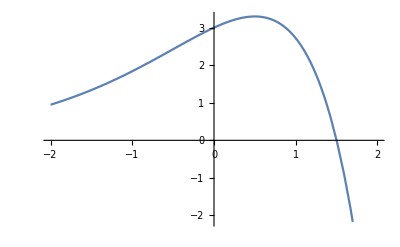

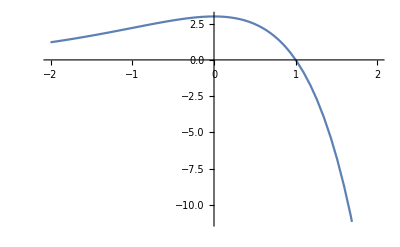

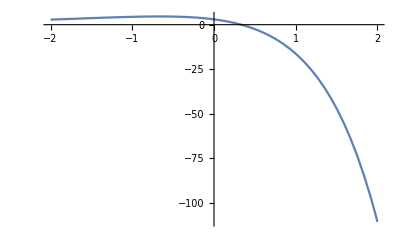

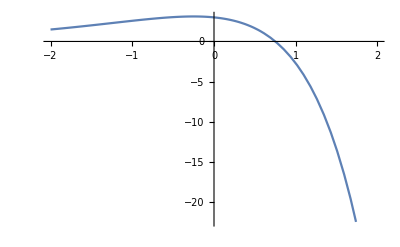

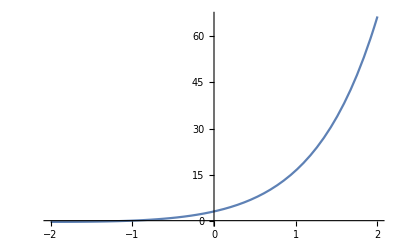

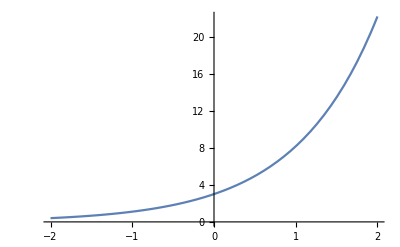

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{x,-2,2},PlotRange→Automatic]

```mathematica
p1=Plot[Evaluate[y[x]/.sol], {x,-2,2}]
p2=Plot[Evaluate[y[x]/.sol1], {x,-2,2}]
p3=Plot[Evaluate[y[x]/.sol2], {x,-2,2}]
p4=Plot[Evaluate[y[x]/.sol3], {x,-2,2}]
p5=Plot[Evaluate[y[x]/.sol4], {x,-2,2}]
p6=Plot[Evaluate[y[x]/.sol5], {x,-2,2}]
Show[{p1, p2 , p3,p4, p5, p6}  , {x,-2,2},PlotRange->Automatic]
```